Your Title Here

```mathematica
θ=60°;
```

```mathematica
colA=Blue;colS=RGBColor[0,0.6,0];colC=RGBColor[0.8,0,0.01];colF=RGBColor[1,0.4,0];colM=Purple;
```

```mathematica
(*phase boundaries*)
```

```mathematica
phase1={{0.09,0},{0.17,0.13},{0.28,0.3},{0.41,0.44},{0.55,0.47},{0.7,0.42},{0.83,0.26},{0.98,0}};
```

```mathematica
phase2={{0.0545,0},{0.136,0.134},{0.226,0.267},{0.3405,0.36},{0.534,0.398},{0.673,0.338},{0.7925,0.232},{0.956,0}};
```

```mathematica
phase3={{0.098,0},{0.172,0.126},{0.2285,0.213},{0.422,0.338},{0.55,0.352},{0.7055,0.284},{0.7925,0.205},{0.9155,0}};
```

```mathematica
phase4={{0.07,0},{0.14,0.14},{0.26,0.35},{0.42,0.56},{0.56,0.59},{0.7,0.42},{0.82,0.24},{0.95,0}};
```

```mathematica
phase5={{0,0},{0.12,0.15},{0.23,0.32},{0.34,0.45},{0.6,0.5},{0.69,0.42},{0.77,0.3},{0.93,0}};
```

```mathematica
(*tie lines*)
```

```mathematica
tie1={Line[{{0.12,0.052},{0.93,0.078}}],Line[{{0.16,0.104},{0.88,0.173}}],Line[{{0.2,0.173},{0.83,0.26}}],Line[{{0.26,0.268},{0.77,0.346}}],Line[{{0.34,0.372},{0.67,0.433}}]};
```

```mathematica
tie2={Line[{{0.1,0.07},{0.9,0.09}}],Line[{{0.13,0.12},{0.84,0.17}}],Line[{{0.17,0.18},{0.77,0.25}}],Line[{{0.23,0.28},{0.65,0.36}}]};
```

```mathematica
tie3={Line[{{0.11,0.03},{0.89,0.06}}],Line[{{0.15,0.09},{0.86,0.11}}],Line[{{0.2,0.18},{0.78,0.22}}],Line[{{0.28,0.27},{0.65,0.32}}]};
```

```mathematica
tie4={Line[{{0.1,0.06},{0.9,0.1}}],Line[{{0.14,0.15},{0.84,0.21}}],Line[{{0.2,0.26},{0.75,0.35}}],Line[{{0.28,0.37},{0.67,0.46}}],Line[{{0.37,0.51},{0.6,0.56}}]};
```

```mathematica
tie5={Line[{{0.06,0.07},{0.87,0.11}}],Line[{{0.11,0.13},{0.83,0.2}}],Line[{{0.16,0.22},{0.76,0.32}}],Line[{{0.23,0.33},{0.69,0.41}}],Line[{{0.33,0.44},{0.61,0.5}}]};
```

```mathematica
(*ternary phase diagram base*)
```

```mathematica
diagram=Graphics[{
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{0.5,√3/2},{1,0}}]},

{(*A*)colA,Text[Style[100*#,16],{1-#/2,#*√3/2},{-2,0}],
(*B*)colS,Text[Rotate[Style[100*(1-#),16],-θ],{#/2,#*√3/2},{1,-1}],
(*C*)colC,Text[Rotate[Style[100*#,16],θ],{#,0},{0,1.5}]}&/@Range[0.1,0.9,0.1],

Text[Rotate[Style["solute",17,colA],-θ],{0.75,√3/4},{-3,0}],
Text[Rotate[Style["solvent",17,colS],θ],{0.25,√3/4},{3,0}],
Text[Style["carrier",17,colC],{0.5,0},{0,5}],

Text[Style["A",20,colA],{0.5,√3/2},{0,-1.2}],
Text[Style["C",20,colC],{1,0},{-2,0}],
Text[Style["S",20,colS],{0,0},{2,0}],

(*phase line*)
(*{Thick,Line[{#,phase[#]}&/@Range[0.08,0.98,0.01]]},*)
}];
```

```mathematica
(*drid lines*)
```

```mathematica
gridlines=Graphics[{GrayLevel@0.65,
Line[{{#/2,#*√3/2},{1-#/2,#*√3/2}}],Line[{{#,0},{#/2,#*√3/2}}],Line[{{1-#,0},{1-#/2,#*√3/2}}]
}&/@Range[0.05,0.95,0.05]];
```

```mathematica
pt1[pt_,col_]:={PointSize@0.025,col,Point@pt};
```

```mathematica
pt2[pt_,col_]:={PointSize@0.025,col,Point@pt,PointSize@0.015,White,Point@pt};
```

```mathematica
Manipulate[
Module[{part,phase,tie},
SeedRandom[reset];
part=RandomInteger[{1,5}];
phase={phase1,phase2,phase3,phase4,phase5}[[part]];
tie={tie1,tie2,tie3,tie4,tie5}[[part]];

Show[gridlines,diagram,ImageSize->{500,400},Epilog->{
{Thick,Line[{#,Interpolation[phase][#]}&/@Range[phase[[1,1]],phase[[-1,1]],0.01]],tie},
}]
],
Button[" new phase line ",If[reset<1000,reset=reset+1,reset=reset-1],ImageSize->Medium],
Control[{{reset,1},1,1000,1,None}],
SaveDefinitions->True]
```

```mathematica
Manipulate[
Module[{part,phase},
SeedRandom[reset];
part=RandomInteger[{1,5}];
phase={phase1,phase2,phase3,phase4,phase5}[[part]];

p1={p1[[1]],Interpolation[phase5][p1[[1]]]};
p2={p2[[1]],Interpolation[phase5][p2[[1]]]};

Column[{
Show[gridlines,diagram,ImageSize->{500,400},Epilog->{
{Thick,Line[{#,Interpolation[phase5][#]}&/@Range[phase5[[1,1]],phase5[[-1,1]],0.01]]},tie5
}],
NumberForm[#,{2,2}]&/@{p1,p2}
}]
],
Button[" new phase line ",If[reset<1000,reset=reset+1,reset=reset-1],ImageSize->Medium],
Control[{{reset,1},1,1000,1,None}],
Control[{{p1,{0.1,0.1*√3/2}},Locator}],Control[{{p2,{0.9,0.1*√3/2}},Locator}],
SaveDefinitions->True]
```

```mathematica
tie2={Thick,Line[{{0.1,0.07},{0.9,0.09}}],Line[{{0.13,0.12},{0.84,0.17}}]};
```

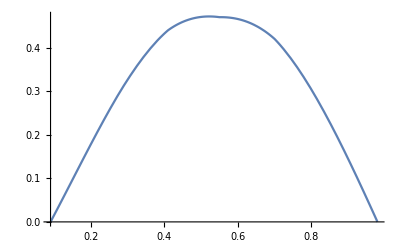

```mathematica
Plot[Interpolation[phase1][x],{x,phase1[[1,1]],phase1[[-1,1]]}]
```

```mathematica
Line[{#,Interpolation[phase1][#]}&/@Range[phase1[[1,1]],phase1[[-1,1]],0.1]]
```

{{0.09,0.},{0.19,0.162525},{0.29,0.313583},{0.39,0.424339},{0.49,0.469343},{0.59,0.467458},{0.69,0.427206},{0.79,0.317936},{0.89,0.162327}}

```mathematica
Manipulate[
Column[{
Grid@{{
Show[gridlines,diagram,ImageSize->{500,400},Epilog->{
{PointSize@0.02,Blue,Point@phase1,Green,Point@phase2,Red,Point@phase3,Purple,Point@phase4},

If[points,{PointSize@0.025,Point@{p1,p2,p3,p4,p5,p6,p7,p8}}],
Line[{#,Interpolation[{p1,p2,p3,p4,p5,p6,p7,p8}][#]}&/@Range[p1[[1]],p8[[1]],0.01]]
}],
Text@Style[Grid[{{1,p1},{2,p2},{3,p3},{4,p4},{5,p5},{6,p5},{7,p7},{8,p8}}],17]
}},
NumberForm[#,{2,2}]&/@{p1,p2,p3,p4,p5,p6,p7,p8}
}],
Grid@{{
Button[" reset ",If[reset<1000,reset=reset+1,reset=reset-1],ImageSize->Medium],
Control[{{points,True,"show points"},{True,False}}],
Control[{{reset,1},1,100,1,None}],
Control[{{p1,{0.09,0}},Locator,Appearance->None}],Control[{{p2,{0.17,0.13}},Locator,Appearance->None}],Control[{{p3,{0.28,0.3}},Locator,Appearance->None}],Control[{{p4,{0.41,0.44}},Locator,Appearance->None}],Control[{{p5,{0.55,0.47}},Locator,Appearance->None}],Control[{{p6,{0.7,0.42}},Locator,Appearance->None}],Control[{{p7,{0.83,0.26}},Locator,Appearance->None}],Control[{{p8,{0.98,0}},Locator,Appearance->None}]
}},
SaveDefinitions->True]
```

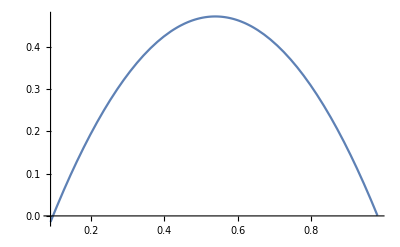

```mathematica
Module[{data,func},
data={{0.09,0},{0.17,0.13},{0.28,0.3},{0.41,0.44},{0.55,0.47},{0.7,0.42},{0.83,0.26},{0.98,0}};

func[z_]:=Fit[data,{1,x,x^2},x]/.x->z;

Plot[func[z],{z,data[[1,1]],data[[-1,1]]}]
]
```

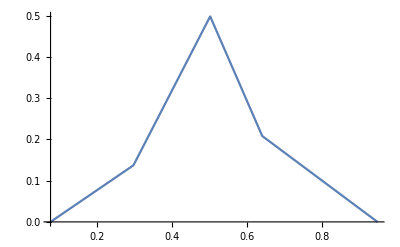





```mathematica
Module[{data,func},
data={
{RandomReal[{0,0.1}],0},
{RandomReal[{0.2,0.3}],RandomReal[{0.1,0.3}]},
{RandomReal[{0.45,0.55}],RandomReal[{0.4,0.7}]},
{RandomReal[{0.6,0.8}],RandomReal[{0.1,0.3}]},
{RandomReal[{0.9,1}],0}
};

ListPlot[data,Joined->True];

Plot[Quiet@Interpolation[data,InterpolationOrder->1][x],{x,data[[1,1]],data[[-1,1]]}]
]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX